### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
{timedata,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}];
timedata
```

{u1==u3&&u3≥u30,u2==u5&&u32≤u5,u4==u9&&u7==u9,u11==u8&&u6==u8,u10==u15&&u13==u15,u12==u17&&u14==u17,u16==u19&&u19≤u21,u18==u23&&u23≤u25,u20==u24&&u24≤u27}

u1==u3&&u3≥u30&&u2==u5&&u32≤u5&&u4==u9&&u7==u9&&u11==u8&&u6==u8&&u10==u15&&u13==u15&&u12==u17&&u14==u17&&u16==u19&&u19≤u21&&u18==u23&&u23≤u25&&u20==u24&&u24≤u27

jt11+jt9==200000-jt12+jt13+jt18-jt22+jt23&&jt15+jt17==-200020+jt14-jt18+jt19+jt20+jt22-jt23&&jt3+jt5==-jt12+jt19+jt20&&jt21+jt23==jt13+jt18-jt22+jt23&&jt1+jt6==jt13+jt14&&jt19+jt24==-200020+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23&&jt27+jt29==jt17+jt18&&jt12+jt7==jt19+jt20&&jt33+jt35==-200020+jt14+jt16-jt17-jt18+jt20+jt22&&jt31+jt36==jt17+jt18+jt28-jt29&&jt29+jt30+jt41==jt29+jt30&&jt45+jt47==jt45&&jt26+jt28==jt14+jt16-jt25+jt28&&jt29+jt30+jt40+jt53==jt29+jt30+jt40&&jt45+jt46+jt54==jt45+jt46&&jt11+jt9≥0&&jt3+jt5≥0&&jt15+jt17≥0&&jt1+jt6≥0&&jt21+jt23≥0&&jt12+jt7≥0&&jt19+jt24≥0&&jt13+jt18≥0&&jt27+jt29≥0&&jt14+jt16≥0&&jt33+jt35≥0&&jt20+jt22≥0&&jt31+jt36≥0&&jt25+jt30≥0&&jt29+jt30+jt41≥0&&jt26+jt28≥0&&jt45+jt47≥0&&200020-jt14-jt16+jt25-jt28+jt29+jt30+jt45≥0&&jt29+jt30+jt40+jt53≥0&&jt37+jt42≥0&&jt38+jt40≥0&&jt45+jt46+jt54≥0&&jt43+jt48≥0&&jt44+jt46≥0&&jt50+jt52≥0&&200000-jt12+jt13+jt18-jt22+jt23≥0&&-200020+jt14-jt18+jt19+jt20+jt22-jt23≥0&&200020-jt12-jt14+jt18-jt22+jt23≥0&&-200000+jt12+jt14-jt18+jt22-jt23≥0&&-jt12+jt19+jt20≥0&&jt13+jt18-jt22+jt23≥0&&200000-jt12≥0&&jt12≥0&&jt13≥0&&jt14≥0&&-200020+jt14-jt17-jt18+jt19+jt20+jt22-jt23≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt13+jt18-jt22≥0&&jt22≥0&&jt23≥0&&-200020+jt14+jt16-jt17-jt18+jt20+jt22-jt23≥0&&jt25≥0&&jt14+jt16-jt25≥0&&jt17+jt18-jt29≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt20+jt22-jt32≥0&&jt32≥0&&-200020+jt14+jt16+jt28-jt29+jt32-jt45≥0&&200020-jt14-jt16+jt25-jt28+jt29+jt30-jt32+jt45≥0&&-jt17-jt18+jt20+jt22-jt28+jt29-jt32+jt45≥0&&jt17+jt18-jt20-jt22+jt28-jt29+jt32≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37≥0&&jt29+jt30≥0&&jt40≥0&&jt43≥0&&200020-jt14-jt16+jt25-jt28+jt29+jt30-jt43+jt45≥0&&jt45≥0&&jt46≥0&&jt45+jt46≥0&&jt37+jt42-jt45-jt46≥0&&jt29+jt30+jt40≥0&&-jt29-jt30-jt40+jt43+jt48≥0&&u1≥u29&&u31≤u2&&u16≤u21&&u18≤u25&&u20≤u27

{j2,j4,j29,j1,j6,j31,j3,j8,j10,j5,j7,j12,j9,j14,j16,j11,j13,j18,j15,j20,j22,j17,j24,j26,j19,j23,j28,j30,j32,u22,u26,u28,u3,u5,u7,u9,u6,u8,u13,u15,u14,u17,u19,u23,u24,jt10,jt2,jt4,jt41,jt42,jt47,jt48,jt53,jt54,jt8,u30,u32,j21,j25,j27,jt1,jt11,jt15,jt21,jt24,jt26,jt27,jt3,jt31,jt33,jt35,jt36,jt38,jt44,jt5,jt50,jt52,jt6,jt7,jt9,jt34,jt39,jt49,jt51}

j1==jt1+jt2&&j3==jt3+jt4&&j30==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j32==jt11+jt12&&j4==jt13+jt14&&j7==jt15+jt16&&j9==jt17+jt18&&j6==jt19+jt20&&j8==jt21+jt22&&j11==jt23+jt24&&j10==jt25+jt26&&j13==jt27+jt28&&j15==jt29+jt30&&j12==jt31+jt32&&j14==jt33+jt34&&j17==jt35+jt36&&j16==jt37+jt38&&j19==jt39+jt40&&j21==jt41+jt42&&j18==jt43+jt44&&j23==jt45+jt46&&j25==jt47+jt48&&j20==jt49+jt50&&j24==jt51+jt52&&j27==jt53+jt54

jt11+jt9==200000-jt12+jt13+jt18-jt22+jt23&&jt15+jt17==-200020+jt14-jt18+jt19-jt2+jt20+jt22-jt23&&jt3+jt5==-jt10-jt12+jt19+jt20&&jt21+jt23==jt13+jt18-jt22+jt23&&jt1+jt6==jt13+jt14&&jt19+jt24==-200020+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23&&jt27+jt29==jt17+jt18&&jt12+jt7==jt19+jt20&&jt33+jt35==-200020+jt14+jt16-jt17-jt18+jt20+jt22&&jt31+jt36==jt17+jt18+jt28-jt29&&jt39+jt41==jt29+jt30&&jt25+jt30==200020-jt14-jt16+2 jt25-jt28+jt29+2 jt30-jt32-jt34+jt45&&jt45+jt47==-200020+jt14+jt16-jt25+jt28-jt29-jt30+jt32+jt34&&jt26+jt28==jt14+jt16-jt25+jt28&&jt51+jt53==jt29+jt30+jt40&&0==jt29+jt30-jt39&&jt49+jt54==jt45+jt46&&0==-200020+jt14+jt16-jt25+jt28-jt29-jt30+jt32+jt34-jt45&&jt37+jt42==jt37+jt42+jt45+jt46-jt49&&jt43+jt48==jt29+jt30+jt40+jt43+jt48-jt51&&0==jt39+jt40+jt45+jt46-jt49-jt51

0.360266

```mathematica
d2e["InitRules"]
```

<|j2→jt3+jt5,j4→jt1+jt6,j29→jt2+jt4,j1→jt11+jt9,j6→jt12+jt7,j31→jt10+jt8,j3→jt15+jt17,j8→jt13+jt18,j10→jt14+jt16,j5→jt21+jt23,j7→jt19+jt24,j12→jt20+jt22,j9→jt27+jt29,j14→jt25+jt30,j16→jt26+jt28,j11→jt33+jt35,j13→jt31+jt36,j18→jt32+jt34,j15→jt39+jt41,j20→jt37+jt42,j22→jt38+jt40,j17→jt45+jt47,j24→jt43+jt48,j26→jt44+jt46,j19→jt51+jt53,j23→jt49+jt54,j28→jt50+jt52,j30→20,j32→200000,u22→u21,u26→u25,u28→u27,u3→u1,u5→u2,u7→u4,u9→u4,u6→u11,u8→u11,u13→u10,u15→u10,u14→u12,u17→u12,u19→u16,u23→u18,u24→u20,jt10→0,jt2→0,jt4→-jt2,jt41→jt29+jt30-jt39,jt42→0,jt47→-200020+jt14+jt16-jt25+jt28-jt29-jt30+jt32+jt34-jt45,jt48→0,jt53→jt39+jt40-jt51,jt54→jt45+jt46-jt49,jt8→-jt10,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→200000-jt12+jt13+jt18-jt22+jt23,jt11→200000-jt12,jt15→-200020+jt14-jt17-jt18+jt19+jt20+jt22-jt23,jt21→jt13+jt18-jt22,jt24→-200020+jt14+jt16-jt17-jt18+jt20+jt22-jt23,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-200020+jt14-jt18+jt19+jt20+jt22-jt23,jt31→jt20+jt22-jt32,jt33→jt25+jt30-jt34,jt35→-200020+jt14+jt16-jt17-jt18+jt20+jt22-jt25-jt30+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt44→jt32+jt34-jt43,jt5→200020-jt12-jt14+jt18-jt22+jt23,jt50→jt37+jt42-jt49,jt52→jt43+jt48-jt51,jt6→-200000+jt12+jt14-jt18+jt22-jt23,jt7→-jt12+jt19+jt20,jt9→jt13+jt18-jt22+jt23,jt34→200020-jt14-jt16+jt25-jt28+jt29+jt30-jt32+jt45,jt39→jt29+jt30,jt49→jt45+jt46,jt51→jt29+jt30+jt40|>

```mathematica
<|aa->3,aa->4|>
```

<|aa→4|>

```mathematica
d2e["AllEq"]
```

j1==jt1+jt2&&j3==jt3+jt4&&j30==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j32==jt11+jt12&&j4==jt13+jt14&&j7==jt15+jt16&&j9==jt17+jt18&&j6==jt19+jt20&&j8==jt21+jt22&&j11==jt23+jt24&&j10==jt25+jt26&&j13==jt27+jt28&&j15==jt29+jt30&&j12==jt31+jt32&&j14==jt33+jt34&&j17==jt35+jt36&&j16==jt37+jt38&&j19==jt39+jt40&&j21==jt41+jt42&&j18==jt43+jt44&&j23==jt45+jt46&&j25==jt47+jt48&&j20==jt49+jt50&&j24==jt51+jt52&&j27==jt53+jt54&&j30==20&&j32==200000&&u22==200&&u26==100&&u28==0&&-u29+u30==0&&-u31+u32==0&&-u21+u22==0&&-u25+u26==0&&-u27+u28==0

```mathematica
uvars=d2e["uvars"];
us=Values@uvars;
jvars=d2e["jvars"];
js=Values@jvars;
jtvars=d2e["jtvars"];
jts=Values@jtvars;
```

```mathematica
system = d2e["EqAllAll"]&&d2e["EqCriticalCase"];
rules = d2e["InitRules"];
{system,rules}=CleanEqualitiesOperator[d2e][{system,rules}];
```

```mathematica
CleanEqualitiesOperator[d2e][{d2e["EqCriticalCase"],<||>}]
```

{True,<|jt36→-jt13+jt14+jt16-jt18+jt19-jt20-jt22+jt24+jt25-jt27-jt29+jt30-jt31+jt33+jt35,jt54→jt13-jt14-jt16+jt18-jt19+jt20+jt22-jt24-jt26+jt27-jt28+jt29+jt32-jt33+jt34-jt35-jt37+jt39+jt41-jt42+jt43-jt45-jt47+jt48-jt49+jt51+jt53,jt9→-jt1-jt11+jt12-jt13+jt15+jt17-jt18+jt19-jt21-jt23+jt24+jt3+jt5-jt6+jt7,u10→-jt1-jt14+jt15-jt16+jt17+jt27+jt29-jt6+u1,u11→-jt1-jt13+jt15+jt17-jt18+jt19+jt24-jt6+u1,u12→-jt1-jt13+jt15+jt17-jt18+jt19-jt20-jt22+jt24+jt33+jt35-jt6+u1,u16→-jt1-jt14+jt15-jt16+jt17-jt26+jt27-jt28+jt29+jt39+jt41-jt6+u1,u18→-jt1-jt13+jt15+jt17-jt18+jt19-jt20-jt22+jt24-jt32+jt33-jt34+jt35+jt45+jt47-jt6+u1,u2→-jt1+jt12-jt13+jt15+jt17-jt18+jt19-jt21-jt23+jt24-jt6+jt7+u1,u20→-jt1-jt14+jt15-jt16+jt17-jt26+jt27-jt28+jt29-jt37+jt39+jt41-jt42+jt51+jt53-jt6+u1,u4→-jt1+jt15+jt17-jt6+u1|>}

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
(List@@({First@#,Last@#}&/@system)//Flatten//Variables)//AbsoluteTiming
```

{0.001657,{jt12,jt13,jt14,jt18,jt19,jt20,jt22,jt25,jt26,jt28,jt30,jt32,jt34,jt37,jt43,jt45,jt49,u18,u29,u31}}

```mathematica
system/.{0->1,Plus->Times, GreaterEqual->Times,Equal->Times,LessEqual->Times,Or->Times,And->Times}//Variables//AbsoluteTiming
```

{0.002191,{jt12,jt13,jt14,jt18,jt19,jt20,jt22,jt25,jt26,jt28,jt30,jt32,jt34,jt37,jt43,jt45,jt49,u18,u29,u31}}

```mathematica
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
getVar[system]//AbsoluteTiming
```

{0.000905,{jt12,jt19,jt20,jt32,jt34,jt45,jt13,jt14,jt18,jt25,jt26,jt22,jt30,jt28,jt37,jt43,jt49,u18,u29,u31}}

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
Reduce[Exists[jjj[[1]],jjj[[1]]+jjj[[2]]==0]]
```

True

```mathematica
getcriticalequations[list_]:= list[[3]]
```

```mathematica
colapse/@Subsets[eqsvars,{2}]
```

{{jt12,jt19,jt20,jt32,jt34,jt45},{{jt12,jt19,jt20,jt32,jt34,jt45},{jt13,jt14,jt32,jt34,jt45}},{{jt12,jt19,jt20,jt32,jt34,jt45},{jt13,jt14}},{jt12,jt19,jt20,jt32,jt34,jt45},{jt12,jt19,jt20,jt32,jt34,jt45},4361,{{jt32,jt34,jt43,u18},{jt37,jt49,jt43,jt49,u18}},{jt32,jt34,jt37,jt43,jt45,jt49,jt43,jt49,u18},{{jt45,jt49,u18},{jt37,jt49,jt43,jt49,u18}},{jt32,jt34,jt37,jt43,jt45,jt49,jt43,jt49,u18},{jt32,jt34,jt37,jt43,jt45,jt49,jt43,jt49,u18}}
 |  |  |  |

```mathematica
Select[%,Length[#]===1&]
```

{}

```mathematica
eqsvars=DeleteDuplicates[getVar/@List@@system]
```

{{jt12,jt19,jt20,jt32,jt34,jt45},{jt12,jt19,jt20},{jt13,jt14,jt32,jt34,jt45},{jt13,jt14},{jt19,jt20,jt32,jt34,jt45},{jt19,jt20},{jt13,jt18,jt32,jt34,jt45},{jt13,jt18},{jt25,jt26,jt32,jt34,jt45},{jt25,jt26},{jt20,jt22,jt32,jt34,jt45},{jt20,jt22},{jt25,jt30,jt32,jt34,jt45},{jt25,jt30},{jt26,jt28,jt32,jt34,jt45},{jt26,jt28},{jt45},{jt32,jt34},{jt32,jt34,jt37,jt43,jt45,jt49},{jt37},{jt32,jt34,jt43,jt45,jt49},{jt49},{jt43},{jt12,jt13,jt14,jt19,jt20,jt32,jt34,jt45},{jt12},{jt13},{jt14},{jt13,jt14,jt18,jt25,jt26,jt32,jt34,jt45},{jt14,jt25,jt26},{jt18,jt25,jt26,jt32,jt34,jt45},{jt18},{jt19},{jt20},{jt13,jt18,jt22},{jt22},{jt13,jt18,jt19,jt20,jt22,jt32,jt34,jt45},{jt13,jt18,jt19,jt32,jt34,jt45},{jt25},{jt26},{jt25,jt28,jt30,jt32,jt34,jt45},{jt28},{jt26,jt28,jt30,jt32,jt34,jt45},{jt30},{jt20,jt22,jt32},{jt32},{jt25,jt30,jt34},{jt34},{jt20,jt22,jt25,jt30,jt32,jt34,jt45},{jt26,jt28,jt37},{jt26,jt28,jt32,jt34,jt37,jt43,jt45,jt49},{jt32,jt34,jt43},{jt45,jt49},{jt37,jt49},{jt32,jt34,jt45,u18,u29},{u31,jt32,jt34,jt45,u18},{jt32,jt34,jt45,u18},{u18},{jt43,jt49,u18},{jt12,jt19,jt20,jt32,jt34,jt45,jt12,jt19,jt20},{jt13,jt14,jt32,jt34,jt45,jt13,jt14},{jt19,jt20,jt32,jt34,jt45,jt19,jt20},{jt13,jt18,jt32,jt34,jt45,jt13,jt18},{jt25,jt26,jt32,jt34,jt45,jt25,jt26},{jt20,jt22,jt32,jt34,jt45,jt20,jt22},{jt25,jt30,jt32,jt34,jt45,jt25,jt30},{jt26,jt28,jt32,jt34,jt45,jt26,jt28},{jt45,jt32,jt34},{jt32,jt34,jt37,jt43,jt45,jt49,jt37},{jt49,jt43},{jt12,jt19,jt20,jt32,jt34,jt45,jt13,jt14,jt32,jt34,jt45},{jt13,jt13,jt14,jt18,jt25,jt26,jt32,jt34,jt45},{jt14,jt18,jt25,jt26,jt32,jt34,jt45},{jt14,jt25,jt26,jt18},{jt19,jt13,jt18,jt22},{jt20,jt13,jt18,jt19,jt20,jt22,jt32,jt34,jt45},{jt22,jt13,jt18,jt19,jt32,jt34,jt45},{jt25,jt25,jt28,jt30,jt32,jt34,jt45},{jt26,jt26,jt28,jt30,jt32,jt34,jt45},{jt28,jt30},{jt20,jt22,jt32,jt25,jt30,jt34},{jt32,jt20,jt22,jt25,jt30,jt32,jt34,jt45},{jt34,jt20,jt22,jt25,jt30,jt32,jt34,jt45},{jt37,jt26,jt28,jt32,jt34,jt45},{jt43,jt45},{jt49,jt32,jt34,jt37,jt43,jt45,jt49},{jt12,jt19,jt20,jt19,jt20,jt32,jt34,jt45},{jt12,jt13,jt14,jt19,jt20,jt32,jt34,jt45,jt32,jt34,jt45,u18,u29},{jt12,jt32,jt34,jt45,u18,u31},{jt26,jt28,jt37,jt32,jt34,jt45,u18},{jt26,jt28,jt32,jt34,jt37,jt43,jt45,jt49,jt32,jt34,jt45,u18},{jt32,jt34,jt43,u18},{jt45,jt49,u18},{jt37,jt49,jt43,jt49,u18},{jt32,jt34,jt37,jt43,jt45,jt49,jt43,jt49,u18}}

```mathematica
SubsetQ
```

```mathematica
Outer[SubsetQ,eqsvars,eqsvars,1]/.{False->0,True->1}//RowReduce//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
GroupBy[DeleteDuplicates[getVar/@List@@system],Subsets]
```

<|{{},{jt12},{jt19},{jt20},{jt32},{jt34},{jt45},{jt12,jt19},{jt12,jt20},{jt12,jt32},{jt12,jt34},{jt12,jt45},{jt19,jt20},38,{jt12,jt32,jt34,jt45},{jt19,jt20,jt32,jt34},{jt19,jt20,jt32,jt45},{jt19,jt20,jt34,jt45},{jt19,jt32,jt34,jt45},{jt20,jt32,jt34,jt45},{jt12,jt19,jt20,jt32,jt34},{jt12,jt19,jt20,jt32,jt45},{jt12,jt19,jt20,jt34,jt45},{jt12,jt19,jt32,jt34,jt45},{jt12,jt20,jt32,jt34,jt45},{jt19,jt20,jt32,jt34,jt45},{jt12,jt19,jt20,jt32,jt34,jt45}}→{{1}},92,1|>
 |  |  |  |

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

```mathematica
critus=Select[us, !FreeQ[#][d2e["EqCriticalCase"]]&];
{{newcrit,rules},nocritu}=FixedPoint[SimpleCrit,{{d2e["EqCriticalCase"],d2e["InitRules"]},critus}];
```

```mathematica
Select[us, !FreeQ[#][d2e["EqCriticalCase"]]&]
```

{u1,u2,u4,u10,u11,u12,u16,u18,u20}

```mathematica
newcrit
```

True

```mathematica
(List@@({First@#,Last@#}&/@(getEqual@(#system/.rules)))//Flatten//Variables)&(*finds all variables involved in the system*)
```

{j21,j25,j27,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt6,jt7,jt8,u21,u25,u27,u29,u30,u31,u32}

```mathematica
List@@({First@#,Last@#}&/@(getEqual[d2e["EqAllAll"]&&d2e["EqCriticalCase"]/.rules]))//Flatten//Variables
```

{j21,j25,j27,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt6,jt7,jt8,u21,u25,u27,u29,u30,u31,u32}

```mathematica
newsys=getNo[js,jts]@getEqual[d2e["EqAllAll"]/.rules]
```

u29==u30&&u31==u32&&u21==200&&u25==100&&u27==0

```mathematica
FirstPosition[us,Function[exp,!FreeQ[exp][newsys]]]
```

Missing[NotFound]

```mathematica
Position[us,u21]
```

{{21}}

```mathematica
us
```

{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32}

```mathematica
CriticalCongestionSolver[d2e]
```

98

$Aborted

```mathematica
Simplify[u31≤u2&&(jt11==0||u2==u31)&&(jt11==200000||u2==u31)&&20+jt15+jt17+u2≥jt13+jt14+u29&&(20+jt1==jt13+jt14||jt13+jt14+u29==20+jt15+jt17+u2)&&(jt1==jt13+jt14||jt13+jt14+u29==20+jt15+jt17+u2)&&1200040+21 jt15+21 jt17+u2≤21 (jt13+jt14)&&20 jt13+20 jt14+u2≤20 (90019+jt15+jt17)&&2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2≤36 jt13+35 jt14+jt25+jt37&&(jt14+jt16+jt28==jt25+jt37||21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2)&&(jt40==0||21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2)&&(1200200+jt1+16 jt15+jt16+15 jt17+jt27+jt28==jt11+15 jt13+15 jt14+jt19+jt21+jt31+jt33+jt43||20 jt13+20 jt14+u2==20 (90019+jt15+jt17))&&(jt1+56 jt13+55 jt14+jt25+jt27+jt37==4000700+jt11+55 jt15+56 jt17+jt19+jt21+jt31+jt33+jt40+jt43||20 jt13+20 jt14+u2==20 (90019+jt15+jt17))&&(56 jt13+55 jt14+jt25+2 jt37==4000700+56 jt15+jt16+56 jt17+jt28+jt40+jt43||36 jt13+35 jt14+jt25+jt37==2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2)&&(15 jt13+14 jt14+jt25+jt43==1000180+15 jt15+jt16+15 jt17+jt28+jt40||36 jt13+35 jt14+jt25+jt37==2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2)]
```

21 (jt13+jt14)≥1200040+21 jt15+21 jt17+u2&&36 jt13+35 jt14+jt25+jt37≥2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2&&20 jt13+20 jt14+u2≤20 (90019+jt15+jt17)&&jt13+jt14+u29==20+jt15+jt17+u2&&u2==u31&&(20 jt13+20 jt14+u2≥20 (90019+jt15+jt17)||(1200200+jt1+16 jt15+jt16+15 jt17+jt27+jt28==jt11+15 jt13+15 jt14+jt19+jt21+jt31+jt33+jt43&&jt1+56 jt13+55 jt14+jt25+jt27+jt37==4000700+jt11+55 jt15+56 jt17+jt19+jt21+jt31+jt33+jt40+jt43))&&(36 jt13+35 jt14+jt25+jt37≤2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2||(56 jt13+55 jt14+jt25+2 jt37==4000700+56 jt15+jt16+56 jt17+jt28+jt40+jt43&&15 jt13+14 jt14+jt25+jt43==1000180+15 jt15+jt16+15 jt17+jt28+jt40))&&(21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2||(jt14+jt16+jt28==jt25+jt37&&jt40==0))

```mathematica
%721//Simplify
```

41 u2==13807180&&41 u29==10807580&&41 u31==13807180&&((jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&((jt11==0&&199700+jt13+jt15+jt25+jt27==jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43)||(20+jt1+jt16+jt28==jt13+jt25+jt37&&41 jt40==3990720)||(4197800/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt11+jt19+jt21+jt31+jt33+jt40==199700+jt13+jt15+jt25+jt27)||jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37))||(jt13+jt14==3000420/41+jt15+jt17&&((jt11==0&&199720+jt1+jt15+jt25+jt27==jt14+jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43)||(199720+jt1+jt15+jt25+jt27==jt11+jt14+jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43)||(jt14+jt16+jt28==jt25+jt37&&41 jt40==3990720)||jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)))

```mathematica
Reduce[%721,Reals]//Simplify
```

41 u2==13807180&&41 u29==10807580&&41 u31==13807180&&((jt11==0&&1202300/41+2 jt1+jt16+jt27+jt28==jt17+jt19+jt21+jt31+jt33+jt43&&7201500/41+2 jt15+jt16+jt17+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&((41 jt40==3990720&&((jt14+jt16+jt28==jt25+jt37&&1200660/41+2 jt13+2 jt25+jt27+2 jt37==jt16+jt17+jt19+jt21+jt28+jt31+jt33+jt43)||(100+jt14+jt16+jt28==jt25+jt43&&100+jt37==jt43&&1192460/41+2 jt13+2 jt25+jt27+jt43==jt16+jt17+jt19+jt21+jt28+jt31+jt33)))||(100+jt37==jt43&&jt14+jt16+jt28+jt40==3986620/41+jt25+jt43&&9173900/41+2 jt13+2 jt25+jt27+jt43==jt16+jt17+jt19+jt21+jt28+jt31+jt33+2 jt40)||(9182100/41+2 jt13+2 jt25+jt27+2 jt37==jt16+jt17+jt19+jt21+jt28+jt31+jt33+2 jt40+jt43&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)))||(41 jt40==3990720&&((jt14+jt16+jt28==jt25+jt37&&jt13+jt25+jt37==3000420/41+jt15+jt16+jt17+jt28)||(100+jt14+jt16+jt28==jt25+jt43&&100+jt37==jt43&&jt13+jt25+jt43==3004520/41+jt15+jt16+jt17+jt28)))||(100+jt37==jt43&&jt14+jt16+jt28+jt40==3986620/41+jt25+jt43&&986200/41+jt13+jt25+jt43==jt15+jt16+jt17+jt28+jt40)||(990300/41+jt13+jt25+jt37==jt15+jt16+jt17+jt28+jt40&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37))

$Aborted

```mathematica
NewReduce[20+jt15+jt17+u31≤jt13+jt14+u1&&(jt11==0||jt13+jt14+u1==20+jt15+jt17+u31)&&(jt11==200000||jt13+jt14+u1==20+jt15+jt17+u31)&&u1≥u29&&(20+jt1==jt13+jt14||u1==u29)&&(jt1==jt13+jt14||u1==u29)&&1200220+20 jt15+20 jt17+u1≤20 (10+jt13+jt14)&&21 jt13+21 jt14+u1≤7 (257200+3 jt15+3 jt17)&&2200400+35 jt15+jt16+35 jt17+jt28+jt40+u1≤35 jt13+34 jt14+jt25+jt37&&(jt14+jt16+jt28==jt25+jt37||1200220+20 jt15+20 jt17+u1==20 (10+jt13+jt14))&&(jt40==0||1200220+20 jt15+20 jt17+u1==20 (10+jt13+jt14))&&(1200200+jt1+16 jt15+jt16+15 jt17+jt27+jt28==jt11+15 jt13+15 jt14+jt19+jt21+jt31+jt33+jt43||21 jt13+21 jt14+u1==7 (257200+3 jt15+3 jt17))&&(jt1+56 jt13+55 jt14+jt25+jt27+jt37==4000700+jt11+55 jt15+56 jt17+jt19+jt21+jt31+jt33+jt40+jt43||21 jt13+21 jt14+u1==7 (257200+3 jt15+3 jt17))&&(56 jt13+55 jt14+jt25+2 jt37==4000700+56 jt15+jt16+56 jt17+jt28+jt40+jt43||35 jt13+34 jt14+jt25+jt37==2200400+35 jt15+jt16+35 jt17+jt28+jt40+u1)&&(15 jt13+14 jt14+jt25+jt43==1000180+15 jt15+jt16+15 jt17+jt28+jt40||35 jt13+34 jt14+jt25+jt37==2200400+35 jt15+jt16+35 jt17+jt28+jt40+u1)]
```

(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&jt11==0&&20+jt1+jt16+jt28==jt13+jt25+jt37&&120+jt1+jt16+jt28==jt13+jt25+jt43&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&20+jt1+jt16+jt28==jt13+jt25+jt37&&41 u1==10807580&&jt1==2999600/41+jt15+jt17&&41 jt40==3990720)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&jt11==0&&20+jt1+jt16+jt28==jt13+jt25+jt37&&120+jt1+jt16+jt28==jt13+jt25+jt43&&jt19+jt21+jt31+jt33==4196980/41+jt13+jt15+jt25+jt27&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&20+jt1+jt16+jt28==jt13+jt25+jt37&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&jt1==2999600/41+jt15+jt17&&41 jt40==3990720)||(jt11==0&&41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&41 u1==10807580&&jt1==2999600/41+jt15+jt17&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&jt11==0&&100+jt37==jt43&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&jt1==2999600/41+jt15+jt17&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&jt11==0&&199700+jt13+jt15+jt25+jt27==jt19+jt21+jt31+jt33+jt40&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&jt19+jt21+jt31+jt33+jt37==4197800/41+jt1+jt15+jt16+jt27+jt28&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&jt13+jt14==3000420/41+jt15+jt17&&199720+jt1+jt15+jt25+jt27==jt14+jt19+jt21+jt31+jt33+jt40&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&jt19+jt21+jt31+jt33+jt37==4197800/41+jt1+jt15+jt16+jt27+jt28&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&41 u29==10807580&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)||(jt11==0&&41 u31==13807180&&41 u29==10807580&&41 u1==10807580&&3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)||(jt11==0&&3000420/41+jt15+jt17==jt13+jt14&&100+jt37==jt43&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28==jt25+jt37&&100+jt14+jt16+jt28==jt25+jt43&&jt14+jt19+jt21+jt31+jt33==4197800/41+jt1+jt15+jt25+jt27&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&41 u29==10807580&&jt14+jt16+jt28==jt25+jt37&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43&&3000420/41+jt15+jt17==jt13+jt14&&41 jt40==3990720)||(jt11==0&&3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28==jt25+jt37&&100+jt14+jt16+jt28==jt25+jt43&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt11==0&&41 u31==13807180&&41 u29==10807580&&jt14+jt16+jt28==jt25+jt37&&41 u1==10807580&&3000420/41+jt15+jt17==jt13+jt14&&41 jt40==3990720)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&20+jt1+jt16+jt28==jt13+jt25+jt37&&120+jt1+jt16+jt28==jt13+jt25+jt43&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&20+jt1+jt16+jt28==jt13+jt25+jt37&&41 u1==10807580&&jt1==2999600/41+jt15+jt17&&41 jt40==3990720)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&20+jt1+jt16+jt28==jt13+jt25+jt37&&120+jt1+jt16+jt28==jt13+jt25+jt43&&jt11+jt19+jt21+jt31+jt33==4196980/41+jt13+jt15+jt25+jt27&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&20+jt1+jt16+jt28==jt13+jt25+jt37&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt1==2999600/41+jt15+jt17&&41 jt40==3990720)||(41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&41 u1==10807580&&jt1==2999600/41+jt15+jt17&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&100+jt37==jt43&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&20+jt1==jt13+jt14&&41 u29==10807580&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt1==2999600/41+jt15+jt17&&jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37)||(jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt11+jt19+jt21+jt31+jt33+jt37==4197800/41+jt1+jt15+jt16+jt27+jt28&&jt11+jt19+jt21+jt31+jt33+jt40==199700+jt13+jt15+jt25+jt27&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt13+jt14==3000420/41+jt15+jt17&&199720+jt1+jt15+jt25+jt27==jt11+jt14+jt19+jt21+jt31+jt33+jt40&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt11+jt19+jt21+jt31+jt33+jt37==4197800/41+jt1+jt15+jt16+jt27+jt28&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&41 u29==10807580&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt13+jt14==3000420/41+jt15+jt17&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)||(41 u31==13807180&&41 u29==10807580&&41 u1==10807580&&3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)||(3000420/41+jt15+jt17==jt13+jt14&&100+jt37==jt43&&jt14+jt16+jt28+jt40==3990720/41+jt25+jt37&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(jt13+jt14==3000420/41+jt15+jt17&&jt14+jt16+jt28==jt25+jt37&&100+jt14+jt16+jt28==jt25+jt43&&jt11+jt14+jt19+jt21+jt31+jt33==4197800/41+jt1+jt15+jt25+jt27&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&41 u29==10807580&&jt14+jt16+jt28==jt25+jt37&&41 u1==10807580&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt13+jt14==3000420/41+jt15+jt17&&41 jt40==3990720)||(3000420/41+jt15+jt17==jt13+jt14&&jt14+jt16+jt28==jt25+jt37&&100+jt14+jt16+jt28==jt25+jt43&&41 jt40==3990720&&41 u1==10807580&&41 u29==10807580&&41 u31==13807180)||(41 u31==13807180&&41 u29==10807580&&jt14+jt16+jt28==jt25+jt37&&41 u1==10807580&&3000420/41+jt15+jt17==jt13+jt14&&41 jt40==3990720)

```mathematica
Reduce[%568]
```

(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt1==-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt11==0)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt11==0&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt11==0&&jt1==-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40&&jt11==7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt1==-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt11==0)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt1==-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt11==0)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt15==-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2&&jt14==3990720/41-jt16+jt25-jt28+jt37-jt40&&jt13==-4591050/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt37+jt40+jt43/2&&jt11==0&&jt1==-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt11==0&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt11==0&&jt1==-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43&&jt11==7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt11==0&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt11==0&&jt1==-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt14==-jt16+jt25-jt28+jt37&&jt13==3000420/41+jt15+jt16+jt17-jt25+jt28-jt37&&jt11==7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt1==-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt11==0)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt37==-100+jt43&&jt15==-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2&&jt14==3986620/41-jt16+jt25-jt28-jt40+jt43&&jt13==-4586950/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2+jt40-jt43/2&&jt11==0&&jt1==-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt15==-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2&&jt14==-jt16+jt25-jt28+jt37&&jt13==-600330/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt37+jt43/2&&jt11==0&&jt1==-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt11==0&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt11==0&&jt1==-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==3004520/41+jt15+jt16+jt17-jt25+jt28-jt43&&jt11==7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43&&jt1==2999600/41+jt15+jt17)||(u31==13807180/41&&u29==10807580/41&&u1==10807580/41&&jt40==3990720/41&&jt37==-100+jt43&&jt15==-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2&&jt14==-100-jt16+jt25-jt28+jt43&&jt13==-596230/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt43/2&&jt11==0&&jt1==-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2)

```mathematica
{ToRules[%569]}
```

{{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt1→-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt11→0},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt11→0,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt11→0,jt1→-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-990300/41+jt15+jt16+jt17-jt25+jt28-jt37+jt40,jt11→7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt1→-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt11→0},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt1→-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt11→0},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt15→-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2,jt14→3990720/41-jt16+jt25-jt28+jt37-jt40,jt13→-4591050/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt37+jt40+jt43/2,jt11→0,jt1→-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt11→0,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt11→0,jt1→-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-986200/41+jt15+jt16+jt17-jt25+jt28+jt40-jt43,jt11→7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt11→0,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt11→0,jt1→-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt14→-jt16+jt25-jt28+jt37,jt13→3000420/41+jt15+jt16+jt17-jt25+jt28-jt37,jt11→7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt1→-4201900/41+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt11→0},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt37→-100+jt43,jt15→-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2,jt14→3986620/41-jt16+jt25-jt28-jt40+jt43,jt13→-4586950/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2+jt40-jt43/2,jt11→0,jt1→-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt15→-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2,jt14→-jt16+jt25-jt28+jt37,jt13→-600330/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt37+jt43/2,jt11→0,jt1→-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt11→0,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt11→0,jt1→-4201900/41-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt14→-100-jt16+jt25-jt28+jt43,jt13→3004520/41+jt15+jt16+jt17-jt25+jt28-jt43,jt11→7201500/41+2 jt15+jt16+jt17-jt19-jt21+jt27+jt28-jt31-jt33-jt43,jt1→2999600/41+jt15+jt17},{u31→13807180/41,u29→10807580/41,u1→10807580/41,jt40→3990720/41,jt37→-100+jt43,jt15→-3600750/41-jt16/2-jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2,jt14→-100-jt16+jt25-jt28+jt43,jt13→-596230/41+jt16/2+jt17/2+jt19/2+jt21/2-jt25-jt27/2+jt28/2+jt31/2+jt33/2-jt43/2,jt11→0,jt1→-601150/41-jt16/2+jt17/2+jt19/2+jt21/2-jt27/2-jt28/2+jt31/2+jt33/2+jt43/2}}

```mathematica
And@@True
```

True

```mathematica
Head@%
```

And

```mathematica
{time,{system,rules}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

0.441754

```mathematica
ccs=system;
```

```mathematica
system=d2e["EqAllAll"]&&d2e["EqCriticalCase"];
```

```mathematica
({s,r}=NewCleanEqualities[{system, <||>}]);//AbsoluteTiming
({s1,r1}=CleanEqualitiesOperator[d2e][system]);//AbsoluteTiming
```

{0.29602,Null}

{0.01021,Null}

```mathematica
s
s1
```

jt1≥0&&41 jt1≥2999600&&jt13+jt14≥3000420/41&&jt13+jt14≥0&&jt1≥jt11&&5200400/41+jt1≥jt11&&jt15+jt16≥0&&jt15+jt16≥799620/41&&jt14+jt16≥3800040/41&&jt14+jt16≥0&&jt1+jt15+jt16≥jt11+jt19+jt21&&4400780/41+jt1+jt15+jt16≥jt11+jt19+jt21&&jt27+jt28≥0&&jt27+jt28≥198880/41&&jt14+jt16+jt28≥3998920/41+jt25&&jt14+jt16+jt28≥jt25&&jt1+jt15+jt16+jt27+jt28≥jt11+jt19+jt21+jt31+jt33&&4201900/41+jt1+jt15+jt16+jt27+jt28≥jt11+jt19+jt21+jt31+jt33&&jt37≥200&&jt37≥0&&jt43≥100&&jt43≥0&&jt1≥0&&jt13+jt14≥3000420/41&&20+jt1≥jt13+jt14&&jt13+jt14≥jt1&&41 jt1≥2999600&&jt1≥jt11&&jt11≥0&&jt11≤200000&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt13+jt14≥3000420/41+jt15&&jt15+jt16≥799620/41+jt13&&jt19≥0&&5200400/41+jt1≥jt11+jt19&&jt21≥0&&jt15+jt16≥799620/41+jt21&&jt1≥jt11+jt21&&jt15+jt16≥jt19&&jt25≥0&&jt14+jt16≥jt25&&jt27≥0&&jt28≥0&&jt14+jt16≥3800040/41+jt27&&jt27+jt28≥198880/41+jt25&&jt31≥0&&4400780/41+jt1+jt15+jt16≥jt11+jt19+jt21+jt31&&jt33≥0&&jt27+jt28≥198880/41+jt33&&jt1+jt15+jt16≥jt11+jt19+jt21+jt33&&jt27+jt28≥jt31&&jt37≥0&&jt14+jt16+jt28≥jt25+jt37&&jt14+jt16+jt28≥3998920/41+jt25&&3990720/41+jt25+jt37≥jt14+jt16+jt28&&jt43≥0&&4201900/41+jt1+jt15+jt16+jt27+jt28≥jt11+jt19+jt21+jt31+jt33+jt43&&jt1+jt15+jt16+jt27+jt28≥jt11+jt19+jt21+jt31+jt33&&jt11+jt19+jt21+jt31+jt33+jt43≥100+jt1+jt15+jt16+jt27+jt28&&jt43≥100&&100+jt37≥jt43&&jt37≥200&&200+jt43≥jt37&&(jt1==0||41 jt1==2999600)&&(jt13+jt14==3000420/41||jt13+jt14==0)&&(jt1==jt11||5200400/41+jt1==jt11)&&(jt15+jt16==0||jt15+jt16==799620/41)&&(jt14+jt16==3800040/41||jt14+jt16==0)&&(jt1+jt15+jt16==jt11+jt19+jt21||4400780/41+jt1+jt15+jt16==jt11+jt19+jt21)&&(jt27+jt28==0||jt27+jt28==198880/41)&&(jt14+jt16+jt28==3998920/41+jt25||jt14+jt16+jt28==jt25)&&(jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33||4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33)&&(jt37==200||jt37==0)&&(jt43==100||jt43==0)&&(jt1==0||jt13+jt14==3000420/41)&&(jt13==0||jt15==0)&&(jt14==0||jt13+jt14==3000420/41+jt15)&&(jt16==0||jt15+jt16==799620/41+jt13)&&(jt19==0||jt21==0)&&(5200400/41+jt1==jt11+jt19||jt1==jt11+jt21)&&(jt15+jt16==799620/41+jt21||jt15+jt16==jt19)&&(jt25==0||jt27==0)&&(jt14+jt16==jt25||jt14+jt16==3800040/41+jt27)&&(jt28==0||jt27+jt28==198880/41+jt25)&&(jt31==0||jt33==0)&&(4400780/41+jt1+jt15+jt16==jt11+jt19+jt21+jt31||jt1+jt15+jt16==jt11+jt19+jt21+jt33)&&(jt27+jt28==198880/41+jt33||jt27+jt28==jt31)&&(jt37==0||jt14+jt16+jt28==3998920/41+jt25)&&(jt43==0||jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33)&&(jt43==100||jt37==200)&&(41 jt1==2999600||jt1==jt11)

jt1≥0&&-2999600/41+jt1≥0&&-3000420/41+jt13+jt14≥0&&jt13+jt14≥0&&jt1-jt11≥0&&5200400/41+jt1-jt11≥0&&jt15+jt16≥0&&-799620/41+jt15+jt16≥0&&-3800040/41+jt14+jt16≥0&&jt14+jt16≥0&&jt1-jt11+jt15+jt16-jt19-jt21≥0&&4400780/41+jt1-jt11+jt15+jt16-jt19-jt21≥0&&jt27+jt28≥0&&-198880/41+jt27+jt28≥0&&-3998920/41+jt14+jt16-jt25+jt28≥0&&jt14+jt16-jt25+jt28≥0&&jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33≥0&&4201900/41+jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33≥0&&-200+jt37≥0&&jt37≥0&&-100+jt43≥0&&jt43≥0&&jt1≥0&&-3000420/41+jt13+jt14≥0&&20+jt1-jt13-jt14≥0&&-jt1+jt13+jt14≥0&&-2999600/41+jt1≥0&&jt1-jt11≥0&&jt11≥0&&200000-jt11≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&-3000420/41+jt13+jt14-jt15≥0&&-799620/41-jt13+jt15+jt16≥0&&jt19≥0&&5200400/41+jt1-jt11-jt19≥0&&jt21≥0&&-799620/41+jt15+jt16-jt21≥0&&jt1-jt11-jt21≥0&&jt15+jt16-jt19≥0&&jt25≥0&&jt14+jt16-jt25≥0&&jt27≥0&&jt28≥0&&-3800040/41+jt14+jt16-jt27≥0&&-198880/41-jt25+jt27+jt28≥0&&jt31≥0&&4400780/41+jt1-jt11+jt15+jt16-jt19-jt21-jt31≥0&&jt33≥0&&-198880/41+jt27+jt28-jt33≥0&&jt1-jt11+jt15+jt16-jt19-jt21-jt33≥0&&jt27+jt28-jt31≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37≥0&&-3998920/41+jt14+jt16-jt25+jt28≥0&&3990720/41-jt14-jt16+jt25-jt28+jt37≥0&&jt43≥0&&4201900/41+jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33-jt43≥0&&jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33≥0&&-100-jt1+jt11-jt15-jt16+jt19+jt21-jt27-jt28+jt31+jt33+jt43≥0&&-100+jt43≥0&&100+jt37-jt43≥0&&-200+jt37≥0&&200-jt37+jt43≥0&&(jt1==0||-2999600/41+jt1==0)&&(-3000420/41+jt13+jt14==0||jt13+jt14==0)&&(jt1-jt11==0||5200400/41+jt1-jt11==0)&&(jt15+jt16==0||-799620/41+jt15+jt16==0)&&(-3800040/41+jt14+jt16==0||jt14+jt16==0)&&(jt1-jt11+jt15+jt16-jt19-jt21==0||4400780/41+jt1-jt11+jt15+jt16-jt19-jt21==0)&&(jt27+jt28==0||-198880/41+jt27+jt28==0)&&(-3998920/41+jt14+jt16-jt25+jt28==0||jt14+jt16-jt25+jt28==0)&&(jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33==0||4201900/41+jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33==0)&&(-200+jt37==0||jt37==0)&&(-100+jt43==0||jt43==0)&&(jt1==0||-3000420/41+jt13+jt14==0)&&(jt13==0||jt15==0)&&(jt14==0||-3000420/41+jt13+jt14-jt15==0)&&(jt16==0||-799620/41-jt13+jt15+jt16==0)&&(jt19==0||jt21==0)&&(5200400/41+jt1-jt11-jt19==0||jt1-jt11-jt21==0)&&(-799620/41+jt15+jt16-jt21==0||jt15+jt16-jt19==0)&&(jt25==0||jt27==0)&&(jt14+jt16-jt25==0||-3800040/41+jt14+jt16-jt27==0)&&(jt28==0||-198880/41-jt25+jt27+jt28==0)&&(jt31==0||jt33==0)&&(4400780/41+jt1-jt11+jt15+jt16-jt19-jt21-jt31==0||jt1-jt11+jt15+jt16-jt19-jt21-jt33==0)&&(-198880/41+jt27+jt28-jt33==0||jt27+jt28-jt31==0)&&(jt37==0||-3998920/41+jt14+jt16-jt25+jt28==0)&&(jt43==0||jt1-jt11+jt15+jt16-jt19-jt21+jt27+jt28-jt31-jt33==0)&&(-100+jt43==0||-200+jt37==0)&&(-2999600/41+jt1==0||jt1-jt11==0)

```mathematica
Clean
```

```mathematica
(system=NewReduce[system])//AbsoluteTiming;
%[[1]]
CleanEqualitiesOperator[d2e]@Reduce[system,Reals]//AbsoluteTiming
```

2.31431

{0.00411,{True,<|j21→0,j25→0,j27→0,jt1→2999600/41,jt10→0,jt11→2999600/41,jt12→5200400/41,jt13→0,jt14→3000420/41,jt15→0,jt16→799620/41,jt17→0,jt18→0,jt19→799620/41,jt2→0,jt20→4400780/41,jt21→0,jt22→0,jt23→0,jt24→0,jt25→0,jt26→3800040/41,jt27→0,jt28→198880/41,jt29→0,jt3→0,jt30→0,jt31→198880/41,jt32→4201900/41,jt33→0,jt34→0,jt35→0,jt36→0,jt37→200,jt38→3990720/41,jt39→0,jt4→0,jt40→0,jt41→0,jt42→0,jt43→100,jt44→4197800/41,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→200,jt51→0,jt52→100,jt53→0,jt54→0,jt6→20,jt7→0,jt8→0,jt9→0,u11→8606780/41,u15→4007120/41,u17→4206000/41,u21→200,u25→100,u27→0,u29→10807580/41,u30→10807580/41,u31→13807180/41,u32→13807180/41,u9→7807160/41|>}}

```mathematica
NewReduce[system]//AbsoluteTiming
```

{2.63862,j21==0&&j25==0&&j27==0&&jt10==0&&41 jt12==5200400&&jt17==0&&jt18==0&&jt2==0&&41 jt20==4400780&&jt22==0&&jt23==0&&jt24==0&&41 jt26==3800040&&jt29==0&&jt3==0&&jt30==0&&41 jt32==4201900&&jt34==0&&jt35==0&&jt36==0&&41 jt38==3990720&&jt39==0&&jt4==0&&jt40==0&&jt41==0&&jt42==0&&41 jt44==4197800&&jt45==0&&jt46==0&&jt47==0&&jt48==0&&jt49==0&&jt5==0&&jt50==200&&jt51==0&&jt52==100&&jt53==0&&jt54==0&&jt6==20&&jt7==0&&jt8==0&&jt9==0&&41 u11==8606780&&41 u15==4007120&&41 u17==4206000&&u21==200&&u25==100&&u27==0&&41 u29==10807580&&41 u30==10807580&&41 u31==13807180&&41 u32==13807180&&41 u9==7807160&&41 jt1==2999600&&41 jt14==3000420&&41 jt11==2999600&&41 jt16==799620&&jt15==0&&jt21==0&&41 jt28==198880&&jt27==0&&jt33==0&&jt37==200&&jt43==100&&jt13==0&&41 jt19==799620&&jt25==0&&41 jt31==198880}

```mathematica
Reduce[system,Reals]//AbsoluteTiming
```

```mathematica
system
```

system

```mathematica
CleanEqualitiesOperator[d2e][{system,{}}]//AbsoluteTiming
```

$Aborted

```mathematica
EqAllAll=Lookup[d2e,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2e,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2e,"BoundaryRules",Print["Need boundary conditions"];];
```

```mathematica
system=EqCriticalCase&&EqAllAll;
rules=InitRules;
```

```mathematica
({system,rules}=CleanEqualitiesOperator[d2e][{system,{}}];)//AbsoluteTiming
```

-j1+j2-u1+u2==0&&-j3+j4-u3+u4==0&&-j5+j6-u5+u6==0&&-j7+j8-u7+u8==0&&j10-j9+u10-u9==0&&-j11+j12-u11+u12==0&&-j13+j14-u13+u14==0&&-j15+j16-u15+u16==0&&-j17+j18-u17+u18==0&&-j19+j20-u19+u20==0&&-j23+j24-u23+u24==0&&j1==jt1+jt2&&j3==jt3+jt4&&j30==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j32==jt11+jt12&&j4==jt13+jt14&&j7==jt15+jt16&&j9==jt17+jt18&&j6==jt19+jt20&&j8==jt21+jt22&&j11==jt23+jt24&&j10==jt25+jt26&&j13==jt27+jt28&&j15==jt29+jt30&&j12==jt31+jt32&&j14==jt33+jt34&&j17==jt35+jt36&&j16==jt37+jt38&&j19==jt39+jt40&&j21==jt41+jt42&&j18==jt43+jt44&&j23==jt45+jt46&&j25==jt47+jt48&&j20==jt49+jt50&&j24==jt51+jt52&&j27==jt53+jt54&&j2==jt3+jt5&&j4==jt1+jt6&&j29==jt2+jt4&&j1==jt11+jt9&&j6==jt12+jt7&&j31==jt10+jt8&&j3==jt15+jt17&&j8==jt13+jt18&&j10==jt14+jt16&&j5==jt21+jt23&&j7==jt19+jt24&&j12==jt20+jt22&&j9==jt27+jt29&&j14==jt25+jt30&&j16==jt26+jt28&&j11==jt33+jt35&&j13==jt31+jt36&&j18==jt32+jt34&&j15==jt39+jt41&&j20==jt37+jt42&&j22==jt38+jt40&&j17==jt45+jt47&&j24==jt43+jt48&&j26==jt44+jt46&&j19==jt51+jt53&&j23==jt49+jt54&&j28==jt50+jt52&&j30==20&&j32==200000&&u22==200&&u26==100&&u28==0&&-u29+u30==0&&-u31+u32==0&&-u21+u22==0&&-u25+u26==0&&-u27+u28==0&&u1==u3&&u2==u5&&u7==u9&&u4==u9&&u6==u8&&u11==u6&&u13==u15&&u10==u15&&u14==u17&&u12==u17&&u16==u19&&u18==u23&&u20==u24&&jt2==0&&jt4==0&&jt8==0&&jt10==0&&jt41==0&&jt42==0&&jt47==0&&jt48==0&&jt53==0&&jt54==0

True

{0.033393,Null}

```mathematica
(Simplify/@system)//Sort
```

j1≥0&&j1≥0&&j1≥j5&&j11≥0&&j11≥jt23&&j11≥jt35&&j13≥0&&41 j13≥11 (18180+j19-j20-j23+j24)&&j19≥0&&j19≥0&&j19≥jt39&&j20≥0&&j20≥0&&j20≥j23&&j23≥0&&j23≥0&&j23≥jt45&&41 j1+j20+j23≥2999700+j19+j24&&41 j1+j20+j23≥2999700+j19+j24&&41 j11+4 (1100095+j20+j23)≥4 (j19+j24)&&4200400+15 j20+56 j23-56 j24≥15 j19&&j24≥0&&j24≥0&&j24≥j19&&j20+j24≥j19+j23&&4000420+56 j19-15 j23+15 j24≥56 j20&&j5≥0&&j5≥0&&j5≥jt23&&200000+j5≥j1&&5200300+j20+j23+41 j5≥j19+j24&&5200300+41 j11+j20+j23+41 j5≥j19+j24+41 (j7+jt23)&&j7≥0&&3 j20+3 j23+41 j7≥3 (266640+j19+j24)&&jt14≥0&&jt17≥0&&jt23≥0&&j7+jt23≥j11&&3 j20+3 j23+41 (j7+jt23)≥799920+3 j19+3 j24+41 j5&&jt26≥0&&41 j13+15 j20+15 j23+41 jt26≥4000420+15 j19+15 j24+41 jt39&&jt29≥0&&j1+j13+(12 j20)/41+(12 j23)/41+jt26+jt29≥3199680/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39&&41 j13+11 j20+11 j23+41 jt29≥199980+11 j19+11 j24+41 jt39&&41 j13+11 j20+11 j23+41 jt26+41 jt29≥199980+11 j19+11 j24+41 jt39&&41 j13+11 j20+11 j23+41 jt26+41 jt29≥199980+11 j19+11 j24+41 jt14+41 jt39&&41 j13+15 j20+15 j23+41 jt26+41 jt29≥4000420+15 j19+15 j24+41 jt39&&41 j13+15 j20+15 j23+41 jt26+41 jt29≥4000420+15 j19+15 j24+41 jt17+41 jt39&&jt35≥0&&j13+jt35≥jt45&&41 j13+11 j20+11 j23+41 jt35≥41 j11+11 (18180+j19+j24)&&jt39≥0&&jt39≥0&&jt39≥jt29&&199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt39≥j13+(11 j20)/41+(11 j23)/41+jt26+jt29&&3200500/41+(12 j19)/41+(12 j24)/41+j7+jt17+jt39≥j13+(12 j20)/41+(12 j23)/41+jt26+jt29&&199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt17+jt39≥j13+(11 j20)/41+(11 j23)/41+jt26+jt29&&199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt17+jt39≥j13+(11 j20)/41+(11 j23)/41+jt26+jt29&&3200500/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39≥j13+(12 j20)/41+(12 j23)/41+jt26+jt29&&3200500/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39≥j1+j13+(12 j20)/41+(12 j23)/41+jt26+jt29&&4000420+15 j19+15 j24+41 jt39≥15 (j20+j23)&&4000420+15 j19+15 j24+41 jt39≥56 j20+15 j23&&4000420+15 j19+15 j24+41 jt39≥15 j20+15 j23+41 jt26&&jt45≥0&&jt45≥0&&jt45≥jt35&&4400380+41 j11+4 j20+4 j23+41 jt45≥41 j13+4 j19+4 j24+41 jt35&&4200400+15 j20+15 j23+41 jt45≥15 (j19+j24)&&4200400+15 j20+15 j23+41 jt45≥15 j19+56 j24&&10801380+21 j20+21 j23+41 u23≥21 j19+21 j24+41 u29&&u23≤100&&j23+u23≤j24&&j20+j23+u23≤200+j19+j24&&20 j19+20 j24+41 u31≤13801080+20 j20+20 j23+41 u23&&(j1==0||41 j1+j20+j23==2999700+j19+j24)&&(j1==0||199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt17+jt39==j13+(11 j20)/41+(11 j23)/41+jt26+jt29)&&(j1==j5||20 j19+20 j24+41 u31==13801080+20 j20+20 j23+41 u23)&&(j1==200000+j5||20 j19+20 j24+41 u31==13801080+20 j20+20 j23+41 u23)&&(j11==0||41 j11+4 (1100095+j20+j23)==4 (j19+j24))&&(j11==j7+jt23||j5==jt23)&&(j13==0||41 j13==11 (18180+j19-j20-j23+j24))&&(j19==0||j20==0)&&(j19==j24||j23+u23==j24)&&(j19==jt39||200+j19+j24==j20+j23+u23)&&(j20==0||jt39==0)&&(j20==j23||j23+u23==j24)&&(j23==0||j19==0)&&(j23==0||j24==0)&&(j23==jt45||u23==100)&&(41 j1+j20+j23==2999700+j19+j24||j5==0)&&(j24==0||jt45==0)&&(15 j19+56 j24==4200400+15 j20+15 j23+41 jt45||u23==100)&&(41 j11+11 (18180+j19+j24)==41 j13+11 j20+11 j23+41 jt35||jt35==jt45)&&(j5==0||j19+j24==5200300+j20+j23+41 j5)&&(5200300+41 j11+j20+j23+41 j5==j19+j24+41 (j7+jt23)||jt23==0)&&(799920+3 j19+3 j24+41 j5==3 j20+3 j23+41 (j7+jt23)||j11==jt23)&&(j7==0||3 (266640+j19+j24)==3 j20+3 j23+41 j7)&&(jt14==0||jt17==0)&&(jt26==0||jt29==0)&&(j1+j13+(12 j20)/41+(12 j23)/41+jt26+jt29==3199680/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39||21 j19+21 j24+41 u29==10801380+21 j20+21 j23+41 u23)&&(41 j13+11 j20+11 j23+41 jt29==199980+11 j19+11 j24+41 jt39||41 j13+15 j20+15 j23+41 jt26==4000420+15 j19+15 j24+41 jt39)&&(41 j13+11 j20+11 j23+41 jt26+41 jt29==199980+11 j19+11 j24+41 jt14+41 jt39||41 j13+15 j20+15 j23+41 jt26+41 jt29==4000420+15 j19+15 j24+41 jt17+41 jt39)&&(41 j13+15 j20+15 j23+41 jt26+41 jt29==4000420+15 j19+15 j24+41 jt39||41 j13+11 j20+11 j23+41 jt26+41 jt29==199980+11 j19+11 j24+41 jt39)&&(j13+jt35==jt45||j11==jt35)&&(jt39==0||4000420+15 j19+15 j24+41 jt39==15 (j20+j23))&&(3200500/41+(12 j19)/41+(12 j24)/41+j7+jt17+jt39==j13+(12 j20)/41+(12 j23)/41+jt26+jt29||199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt39==j13+(11 j20)/41+(11 j23)/41+jt26+jt29)&&(199980/41+(11 j19)/41+(11 j24)/41+j7+jt14+jt17+jt39==j13+(11 j20)/41+(11 j23)/41+jt26+jt29||3200500/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39==j13+(12 j20)/41+(12 j23)/41+jt26+jt29)&&(3200500/41+(12 j19)/41+(12 j24)/41+j7+jt14+jt17+jt39==j1+j13+(12 j20)/41+(12 j23)/41+jt26+jt29||21 j19+21 j24+41 u29==10801380+21 j20+21 j23+41 u23)&&(4000420+15 j19+15 j24+41 jt39==56 j20+15 j23||200+j19+j24==j20+j23+u23)&&(4000420+15 j19+15 j24+41 jt39==15 j20+15 j23+41 jt26||jt29==jt39)&&(jt45==0||15 (j19+j24)==4200400+15 j20+15 j23+41 jt45)&&(4400380+41 j11+4 j20+4 j23+41 jt45==41 j13+4 j19+4 j24+41 jt35||jt35==0)

```mathematica
Sort[Simplify/@ccs]
```

j1≥0&&j1≥j5&&j10≥0&&j10≥jt25&&j11≥0&&j12≥0&&j12≥jt31&&j10+j12≥200020+j11&&j13≥0&&j13≥jt31&&j11+j13≥j17+jt31&&j14≥0&&j14≥jt25&&j10+j12+j14≥200020+j11+j15+jt25&&j15≥0&&200020+j11+j13+j15≥j12+j14&&200020+j11+j13+j15≥j12+j14+j20&&j17≥0&&j12+j14+j17≥j11+j13&&j19≥0&&j19≥j15&&200020+j11+j13+j19≥j12+j14+j20&&3 j12+4 j14+j19≥200020+3 j11+4 j13+j20&&3 j12+4 j14+j17+j19≥200020+3 j11+4 j13+j20+j23&&j2≥0&&j2≥j3&&j20≥0&&j20≥j23&&200020+2 j11+3 j13+2 j20≥2 j12+3 j14+2 j19&&j23≥0&&j23≥j17&&200020+2 j11+3 j13+j20+j23≥2 j12+3 j14+j19&&200020+2 j11+3 j13+j20+j23≥2 j12+3 j14+2 j19&&j3≥0&&20+j3≥j2&&20+j1+j3≥j2&&20+j1+j3≥j2+jt13&&j5≥0&&200000+j5≥j1&&200000+j2+j5≥j1&&200000+j2+j5≥j1+jt19&&j7≥0&&j7≥jt19&&j1+j12+j7≥200000+j11+j2&&j1+j12+j7≥200000+j11+j2+jt13&&20+j1+j3+j7≥j10+j2+jt13&&j5+j7≥j11+jt19&&jt13≥0&&j10+j2+jt13≥20+j1+j3&&j10+j2+jt13≥20+j1+j7&&jt19≥0&&j11+jt19≥j7&&j1+j12+jt19≥200000+j2+j5&&jt25≥0&&j15+jt25≥j14&&200020+j11+j13+j15+jt25≥j10+j12+j14&&jt31≥0&&j17+jt31≥j13&&j14+j17+jt31≥j11+j13&&u1≥u1&&j11+2 j13+u10≤100+j12+2 j14&&j12+j14+u10≤200220+j11+j13&&j12+j14+j19+u10≤200020+j11+j13+j20&&(j1==0||j2==0)&&(j1==0||j3==0)&&(j10==jt25||j14==j15+jt25)&&(j11==0||j12==0)&&(j12==jt31||j13==j17+jt31)&&(j10+j12==200020+j11||j10==0)&&(j13==0||j14==0)&&(j11+j13==j14+j17+jt31||j13==jt31)&&(200220+j11+j13==j12+j14+u10||j15==j19)&&(200220+j11+j13==j12+j14+u10||200020+j11+j13+j15==j12+j14+j20)&&(j10+j12+j14==200020+j11+j13+j15+jt25||j14==jt25)&&(j15==0||200020+j11+j13+j15==j12+j14)&&(j17==0||j11+j13==j12+j14+j17)&&(j17==j23||j11+2 j13+u10==100+j12+2 j14)&&(j19==0||j20==0)&&(j2==0||j5==0)&&(j20==0||j15==0)&&(j20==j23||200020+j11+j13+j20==j12+j14+j19+u10)&&(200020+j11+j13+j20==j12+j14+j19+u10||200020+2 j11+3 j13+j20+j23==2 j12+3 j14+2 j19)&&(j23==0||j19==0)&&(j23==0||200020+2 j11+3 j13+j20+j23==2 j12+3 j14+j19)&&(200020+2 j11+3 j13+j20+j23==2 j12+3 j14+j19||j17==0)&&(200020+3 j11+4 j13+j20+j23==3 j12+4 j14+j17+j19||j11+2 j13+u10==100+j12+2 j14)&&(j3==0||20+j1+j3==j2)&&(20+j1+j3==j2+jt13||20+j1+j7==j10+j2+jt13)&&(20+j1+j3==j10+j2+jt13||j1+j12+j7==200000+j11+j2+jt13)&&(j5==0||j1==200000+j2+j5)&&(j7==0||j1+j12+j7==200000+j11+j2)&&(jt13==0||20+j1+j3+j7==j10+j2+jt13)&&(jt19==0||j11+jt19==j5+j7)&&(j1+jt19==200000+j2+j5||j11+jt19==j7)&&(j1+j12+jt19==200000+j2+j5||j7==jt19)&&(jt25==0||j10+j12+j14==200020+j11+j15+jt25)&&(jt31==0||j11+j13==j17+jt31)

```mathematica
vars = Join[Values[d2e["uvars"]],Values[d2e["jvars"]]]
```

{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32,j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32}

```mathematica
{{fs,fr},fv}=FixedPoint[EliminateVarsStep2,{{system,rules},vars}](*7 halts*)
```

u23

j23==-100+j24&&j19==-100+j20+j23-j24&&u23==100&&u31==1/41 (13805180-20 j19+20 j20+20 j23-20 j24)&&u29==1/41 (10805480-21 j19+21 j20+21 j23-21 j24)

True

j1

j13==1/41 (198880+41 j7+41 jt14+41 jt17-41 jt26-41 jt29+41 jt39)&&j1==2999600/41

True

j5

jt23==0

True

j7

j5==0

True

j11

jt35==0&&jt29==0&&j7==799620/41&&j13==1/41 (3998920-41 jt26)

True

j13

j11==0

True

j19

True

j23

j19==0

True

Missing[NotFound]

Missing[NotFound]

{{((jt17<0&&jt14==3000420/41&&jt45==0&&j23==0)||(jt17==0&&jt14≤3000420/41&&jt45==0&&j23==0))&&-4201900/41≤jt45≤198880/41&&((jt14==3000420/41&&jt17==0&&j13==198880/41)||(jt14==3800040/41&&jt17==-799620/41&&j13==198880/41))&&jt45≥0&&jt14≥0&&jt17≥0&&jt45≥0&&jt45≥0&&(jt14==0||jt17==0),<|j10→799620/41+jt14+jt17,j12→4400780/41,j14→-198880/41+j13,j15→3000420/41-jt14-jt17,j16→6999340/41-jt14-jt17,j17→jt45,j18→4201900/41+jt45,j2→0,j21→0,j22→3990720/41,j25→0,j26→4197800/41,j27→0,j28→300,j29→0,j3→0,j30→20,j31→0,j32→200000,j4→3000420/41,j6→5200400/41,j8→0,j9→-3000420/41+jt14+jt17,jt1→2999600/41,jt10→0,jt11→2999600/41,jt12→5200400/41,jt13→3000420/41-jt14,jt15→-jt17,jt16→799620/41+jt17,jt18→-3000420/41+jt14,jt19→799620/41,jt2→0,jt20→4400780/41,jt21→0,jt22→0,jt24→0,jt25→-3199300/41+j13+jt14+jt17,jt27→-3000420/41+jt14+jt17,jt28→3000420/41+j13-jt14-jt17,jt3→0,jt30→3000420/41-jt14-jt17,jt31→j13-jt45,jt32→4400780/41-j13+jt45,jt33→0,jt34→-198880/41+j13,jt36→jt45,jt37→200,jt38→6991140/41-jt14-jt17,jt4→0,jt40→-3000420/41+jt14+jt17,jt41→0,jt42→0,jt43→100+j23,jt44→4197800/41-j23+jt45,jt46→j23-jt45,jt47→0,jt48→0,jt49→j23,jt5→0,jt50→200-j23,jt51→0,jt52→100+j23,jt53→0,jt54→0,jt6→20,jt7→0,jt8→0,jt9→0,u1→10807580/41,u10→4007120/41,u11→8606780/41,u12→4206000/41,u13→4007120/41,u14→4206000/41,u15→4007120/41,u16→200,u17→4206000/41,u18→100,u19→200,u2→13807180/41,u20→0,u21→200,u22→200,u24→0,u25→100,u26→100,u27→0,u28→0,u3→10807580/41,u30→10807580/41,u32→13807180/41,u4→7807160/41,u5→13807180/41,u6→8606780/41,u7→7807160/41,u8→8606780/41,u9→7807160/41,j20→200,j24→100+j23,u23→100,u29→10807580/41,u31→13807180/41,j1→2999600/41,jt39→3000420/41-jt14-jt17,jt23→0,j5→0,j7→799620/41,jt26→3998920/41-j13,jt29→0,jt35→0,j11→0,j19→0|>},{}}

```mathematica
fv
```

{}

```mathematica
NewReduce[fs]
```

got And: jt17<0&&jt14==3000420/41&&jt45==0&&j23==0

got And: jt14==3000420/41&&jt17==0&&j13==198880/41

first is false

got And: jt14==3800040/41&&jt17==-799620/41&&j13==198880/41

first is false

got And: jt17==0&&jt14≤3000420/41&&jt45==0&&j23==0

got And: jt14==3000420/41&&jt17==0&&j13==198880/41

got And: jt14==3800040/41&&jt17==-799620/41&&j13==198880/41

first is false

got And: 41 jt14==3000420&&jt17==0

got And: 41 jt14==3800040&&jt17==-799620/41

first is false

got And: 41 jt14==3000420&&jt17==0

got And: 41 jt14==3800040&&jt17==-799620/41

first is false

jt17==0&&0≤jt45≤198880/41&&41 jt14==3000420&&41 j13==198880&&0≤jt14≤3000420/41&&((41 j13==198880&&0≤jt45≤198880/41&&jt17≥0&&jt14==0)||(41 j13==198880&&0≤jt45≤198880/41&&0≤jt14≤3000420/41&&jt17==0))&&jt45==0&&jt14≥0&&j23==0

```mathematica
BooleanConvert[fs//Sort,"CNF"]//NewReduce
```

first is false

41 jt14==3000420&&jt17==0&&41 j13==198880&&jt45==0&&j23==0

### got to fix the “got And”!!

```mathematica
NewReduce[fs]
```

got And: jt17<0&&jt14==3000420/41&&jt45==0&&j23==0

got And: jt14==3000420/41&&jt17==0&&j13==198880/41

first is false

got And: jt14==3800040/41&&jt17==-799620/41&&j13==198880/41

first is false

got And: jt17==0&&jt14≤3000420/41&&jt45==0&&j23==0

got And: jt14==3000420/41&&jt17==0&&j13==198880/41

got And: jt14==3800040/41&&jt17==-799620/41&&j13==198880/41

first is false

got And: 41 jt14==3000420&&jt17==0

got And: 41 jt14==3800040&&jt17==-799620/41

first is false

got And: 41 jt14==3000420&&jt17==0

got And: 41 jt14==3800040&&jt17==-799620/41

first is false

jt17==0&&0≤jt45≤198880/41&&41 jt14==3000420&&41 j13==198880&&0≤jt14≤3000420/41&&((41 j13==198880&&0≤jt45≤198880/41&&jt17≥0&&jt14==0)||(41 j13==198880&&0≤jt45≤198880/41&&0≤jt14≤3000420/41&&jt17==0))&&jt45==0&&jt14≥0&&j23==0

```mathematica
ReZAnd[-4201900/41≤jt45≤198880/41&&jt45≥0&&jt14≥0&&jt17≥0&&jt45≥0&&jt45≥0,((jt14==3000420/41&&jt17==0&&j13==198880/41)||(jt14==3800040/41&&jt17==-799620/41&&j13==198880/41))&&(jt14==0||jt17==0),jt17<0]
```

got And: jt14==3000420/41&&jt17==0&&j13==198880/41

first is false

got And: jt14==3800040/41&&jt17==-799620/41&&j13==198880/41

first is false

False

```mathematica
NewReduce[fs]
```

got And: jt17<0&&jt14==3000420/41&&jt45==0&&j23==0

got And: jt17==0&&jt14≤3000420/41&&jt45==0&&j23==0

(-4201900/41≤jt45≤198880/41&&jt45≥0&&jt14≥0&&jt17≥0&&jt45≥0&&jt45≥0&&((jt14==3000420/41&&jt17==0&&j13==198880/41)||(jt14==3800040/41&&jt17==-799620/41&&j13==198880/41))&&(jt14==0||jt17==0)&&jt17<0&&jt14==3000420/41&&jt45==0&&j23==0)||(-4201900/41≤jt45≤198880/41&&jt45≥0&&jt14≥0&&jt17≥0&&jt45≥0&&jt45≥0&&((jt14==3000420/41&&jt17==0&&j13==198880/41)||(jt14==3800040/41&&jt17==-799620/41&&j13==198880/41))&&(jt14==0||jt17==0)&&jt17==0&&jt14≤3000420/41&&jt45==0&&j23==0)

```mathematica
Reduce@%
```

j11==0&&j19==0&&j23==0&&j5==0&&jt17==0&&jt23==0&&jt29==0&&jt35==0&&jt39==0&&jt45==0&&j7==799620/41&&u23==100&&jt26==3800040/41&&jt14==3000420/41&&j24==100&&j20==200&&j13==198880/41&&j1==2999600/41

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
NewReduce[Sort[%21[[2,1]]]]//AbsoluteTiming
NewReduce[ReverseSort[%21[[2,1]]]]//AbsoluteTiming
NewReduce[%21[[2,1]]]//AbsoluteTiming
```

{7.66135,41 j1==2999600&&j11==0&&41 j13==198880&&j19==0&&j20==200&&j23==0&&j24==100&&j5==0&&41 j7==799620&&41 jt14==3000420&&jt17==0&&jt23==0&&41 jt26==3800040&&jt29==0&&jt35==0&&jt39==0&&jt45==0&&u23==100&&41 u29==10807580&&41 u31==13807180}

{26.6443,41 j1==2999600&&j11==0&&41 j13==198880&&j19==0&&j20==200&&j23==0&&j24==100&&j5==0&&41 j7==799620&&41 jt14==3000420&&jt17==0&&jt23==0&&41 jt26==3800040&&jt29==0&&jt35==0&&jt39==0&&jt45==0&&u23==100&&41 u29==10807580&&41 u31==13807180}

{4.04413,j24==100&&jt39==0&&j5==0&&41 j7==799620&&jt17==0&&j11==0&&41 j13==198880&&jt29==0&&jt45==0&&j19==0&&j23==0&&41 jt14==3000420&&jt23==0&&41 jt26==3800040&&jt35==0&&41 u29==10807580&&41 u31==13807180&&u23==100&&41 j1==2999600&&j20==200}

```mathematica
%21[[2,1]]
```

j1≥0&&-2999700/41+j1-j19/41+j20/41+j23/41-j24/41≥0&&199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14+jt17-jt26-jt29+jt39≥0&&3200500/41-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt14+jt17-jt26-jt29+jt39≥0&&j5≥0&&5200300/41-j19/41+j20/41+j23/41-j24/41+j5≥0&&j7≥0&&-799920/41-(3 j19)/41+(3 j20)/41+(3 j23)/41-(3 j24)/41+j7≥0&&-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt26+jt29-jt39≥0&&-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt26+jt29-jt39≥0&&j11≥0&&4400380/41+j11-(4 j19)/41+(4 j20)/41+(4 j23)/41-(4 j24)/41≥0&&j13≥0&&-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41≥0&&jt39≥0&&4000420/41+(15 j19)/41-(15 j20)/41-(15 j23)/41+(15 j24)/41+jt39≥0&&jt45≥0&&4200400/41-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt45≥0&&j19≥0&&j20≥0&&4000420/41+(56 j19)/41-(56 j20)/41-(15 j23)/41+(15 j24)/41≥0&&j23≥0&&j24≥0&&4200400/41-(15 j19)/41+(15 j20)/41+(56 j23)/41-(56 j24)/41≥0&&-j19+j20-j23+j24≥0&&j1≥0&&199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14+jt17-jt26-jt29+jt39≥0&&-3199680/41+j1+j13-(12 j19)/41+(12 j20)/41+(12 j23)/41-(12 j24)/41-j7-jt14-jt17+jt26+jt29-jt39≥0&&3200500/41-j1-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt14+jt17-jt26-jt29+jt39≥0&&-2999700/41+j1-j19/41+j20/41+j23/41-j24/41≥0&&j5≥0&&j1-j5≥0&&200000-j1+j5≥0&&3200500/41-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt17-jt26-jt29+jt39≥0&&jt14≥0&&199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14-jt26-jt29+jt39≥0&&-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41-jt14+jt26+jt29-jt39≥0&&jt17≥0&&-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41-jt17+jt26+jt29-jt39≥0&&-j11+j7+jt23≥0&&5200300/41+j11-j19/41+j20/41+j23/41-j24/41+j5-j7-jt23≥0&&j5-jt23≥0&&-799920/41-(3 j19)/41+(3 j20)/41+(3 j23)/41-(3 j24)/41-j5+j7+jt23≥0&&jt23≥0&&j11-jt23≥0&&-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt29-jt39≥0&&jt26≥0&&-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt26-jt39≥0&&4000420/41+(15 j19)/41-(15 j20)/41-(15 j23)/41+(15 j24)/41-jt26+jt39≥0&&jt29≥0&&-jt29+jt39≥0&&j13+jt35-jt45≥0&&4400380/41+j11-j13-(4 j19)/41+(4 j20)/41+(4 j23)/41-(4 j24)/41-jt35+jt45≥0&&j11-jt35≥0&&-199980/41-j11+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt35≥0&&jt35≥0&&-jt35+jt45≥0&&j20≥0&&4000420/41+(15 j19)/41-(56 j20)/41-(15 j23)/41+(15 j24)/41+jt39≥0&&jt39≥0&&j19-jt39≥0&&j24≥0&&4200400/41-(15 j19)/41+(15 j20)/41+(15 j23)/41-(56 j24)/41+jt45≥0&&jt45≥0&&j23-jt45≥0&&j23≥0&&j20-j23≥0&&j19≥0&&-j19+j24≥0&&10801380/41-(21 j19)/41+(21 j20)/41+(21 j23)/41-(21 j24)/41+u23≥u29&&u31≤13801080/41-(20 j19)/41+(20 j20)/41+(20 j23)/41-(20 j24)/41+u23&&-j19+j20+j23-j24+u23≤200&&u23≤100&&j23-j24+u23≤0&&(j1==0||-2999700/41+j1-j19/41+j20/41+j23/41-j24/41==0)&&(199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14+jt17-jt26-jt29+jt39==0||3200500/41-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt14+jt17-jt26-jt29+jt39==0)&&(j5==0||5200300/41-j19/41+j20/41+j23/41-j24/41+j5==0)&&(j7==0||-799920/41-(3 j19)/41+(3 j20)/41+(3 j23)/41-(3 j24)/41+j7==0)&&(-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt26+jt29-jt39==0||-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt26+jt29-jt39==0)&&(j11==0||4400380/41+j11-(4 j19)/41+(4 j20)/41+(4 j23)/41-(4 j24)/41==0)&&(j13==0||-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41==0)&&(jt39==0||4000420/41+(15 j19)/41-(15 j20)/41-(15 j23)/41+(15 j24)/41+jt39==0)&&(jt45==0||4200400/41-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt45==0)&&(j19==0||j20==0)&&(j23==0||j24==0)&&(j1==0||199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14+jt17-jt26-jt29+jt39==0)&&(3200500/41-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt17-jt26-jt29+jt39==0||199980/41-j13+(11 j19)/41-(11 j20)/41-(11 j23)/41+(11 j24)/41+j7+jt14-jt26-jt29+jt39==0)&&(jt14==0||jt17==0)&&(-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41-jt14+jt26+jt29-jt39==0||-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41-jt17+jt26+jt29-jt39==0)&&(-j11+j7+jt23==0||j5-jt23==0)&&(5200300/41+j11-j19/41+j20/41+j23/41-j24/41+j5-j7-jt23==0||jt23==0)&&(-799920/41-(3 j19)/41+(3 j20)/41+(3 j23)/41-(3 j24)/41-j5+j7+jt23==0||j11-jt23==0)&&(-199980/41+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt29-jt39==0||-4000420/41+j13-(15 j19)/41+(15 j20)/41+(15 j23)/41-(15 j24)/41+jt26-jt39==0)&&(jt26==0||jt29==0)&&(4000420/41+(15 j19)/41-(15 j20)/41-(15 j23)/41+(15 j24)/41-jt26+jt39==0||-jt29+jt39==0)&&(j13+jt35-jt45==0||j11-jt35==0)&&(4400380/41+j11-j13-(4 j19)/41+(4 j20)/41+(4 j23)/41-(4 j24)/41-jt35+jt45==0||jt35==0)&&(-199980/41-j11+j13-(11 j19)/41+(11 j20)/41+(11 j23)/41-(11 j24)/41+jt35==0||-jt35+jt45==0)&&(j20==0||jt39==0)&&(j24==0||jt45==0)&&(j23==0||j19==0)&&(-2999700/41+j1-j19/41+j20/41+j23/41-j24/41==0||j5==0)&&(-3199680/41+j1+j13-(12 j19)/41+(12 j20)/41+(12 j23)/41-(12 j24)/41-j7-jt14-jt17+jt26+jt29-jt39==0||10801380/41-(21 j19)/41+(21 j20)/41+(21 j23)/41-(21 j24)/41+u23-u29==0)&&(3200500/41-j1-j13+(12 j19)/41-(12 j20)/41-(12 j23)/41+(12 j24)/41+j7+jt14+jt17-jt26-jt29+jt39==0||10801380/41-(21 j19)/41+(21 j20)/41+(21 j23)/41-(21 j24)/41+u23-u29==0)&&(j1-j5==0||13801080/41-(20 j19)/41+(20 j20)/41+(20 j23)/41-(20 j24)/41+u23-u31==0)&&(200000-j1+j5==0||13801080/41-(20 j19)/41+(20 j20)/41+(20 j23)/41-(20 j24)/41+u23-u31==0)&&(4000420/41+(15 j19)/41-(56 j20)/41-(15 j23)/41+(15 j24)/41+jt39==0||200+j19-j20-j23+j24-u23==0)&&(j19-jt39==0||200+j19-j20-j23+j24-u23==0)&&(4200400/41-(15 j19)/41+(15 j20)/41+(15 j23)/41-(56 j24)/41+jt45==0||100-u23==0)&&(j23-jt45==0||100-u23==0)&&(j20-j23==0||-j23+j24-u23==0)&&(-j19+j24==0||-j23+j24-u23==0)

```mathematica
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
vars = Join[Values[d2e["uvars"]],(*Reverse*)Values[d2e["jvars"]]];
```

```mathematica
system
```

```mathematica
rules
```

```mathematica
vars
```

{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32,j32,j31,j30,j29,j28,j27,j26,j25,j24,j23,j22,j21,j20,j19,j18,j17,j16,j15,j14,j13,j12,j11,j10,j9,j8,j7,j6,j5,j4,j3,j2,j1}

```mathematica
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
```

u12

j10

$Aborted

0.186051

```mathematica
{time,rules}=AbsoluteTiming@Solver[d2e][alpha=1];
time
```

The error (1-Norm of LHS-RHS) is 3.63043×10^-14

The error is 3.63043×10^-14 which is less than 1.×10^-10

It took 6.46393 seconds to solve!
	The system is True

6.46547

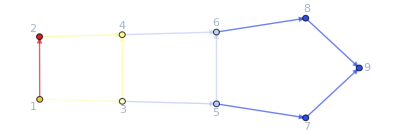

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rules]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

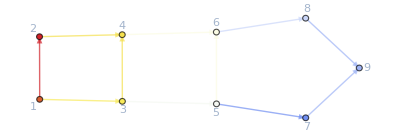

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

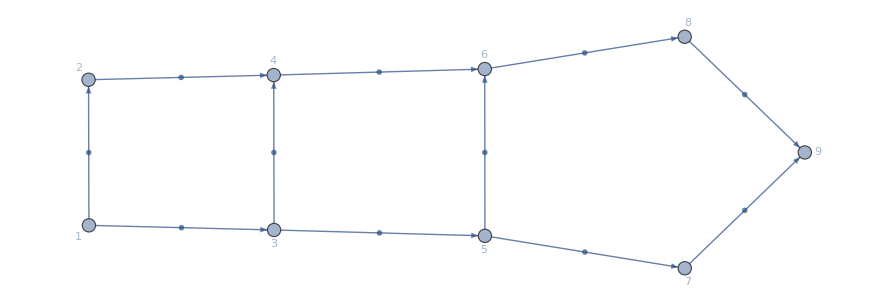

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

length of system: 238

number of alernatives: 80

length of system after eliminating us: 232

new number of alernatives: 76

CCS:
j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)

CCS:
((7 jt79==6&&((jt76==0&&(jt81==0||jt81==0))||(jt76==0&&jt81==0)))||(jt81==0&&((7 jt76==6&&(jt79==0||jt79==0))||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))))&&((jt40==0&&7 jt43==4&&(jt45==0||jt45==0))||(jt45==0&&((7 jt40==4&&(jt43==0||jt43==0))||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))))&&((7 jt64==6&&(jt67==0||jt67==0))||(jt64==2/7&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((7 jt31==6&&((jt28==0&&(jt33==0||jt33==0))||(jt28==0&&jt33==0)))||(jt33==0&&((7 jt28==6&&(jt31==0||jt31==0))||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))))

CCS:
((jt28==0&&7 jt31==6)||(7 jt28==6&&jt31==0)||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))&&((jt40==0&&7 jt43==4)||(7 jt40==4&&jt43==0)||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))&&((7 jt64==6&&jt67==0)||(7 jt64==2&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((jt76==0&&7 jt79==6)||(7 jt76==6&&jt79==0)||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))

55.5666

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

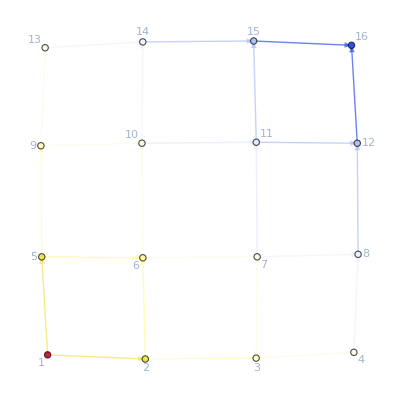

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Solve//FindInstance
```

FindInstance[{{jt28→ConditionalExpression[1/7 (6-7 jt31), 0≤jt31≤6/7],jt40→ConditionalExpression[1/7 (4-7 jt43), 0≤jt43≤4/7],jt64→ConditionalExpression[1/7 (6-7 jt67), 0≤jt67≤4/7],jt76→ConditionalExpression[1/7 (6-7 jt79), 0≤jt79≤6/7]}}]

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,1000,10}]
```

length of system: 231

number of alernatives: 78

length of system after eliminating us: 214

new number of alernatives: 68

CCS:
j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt58==0&&14101 jt61==436000&&(jt63==0||jt63==0))||(jt63==0&&((14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))))&&((14101 jt34==1050900&&jt37==606200/14101)||(jt34==197600/14101&&14101 jt37==1459500)||(14101 jt34≤1050900&&14101 jt34≥197600&&jt34+jt37==1657100/14101))&&((jt46==0&&14101 jt49==1185600&&(jt51==0||jt51==0))||(jt51==0&&((14101 jt46==734400&&jt49==451200/14101)||(14101 jt46≤734400&&jt46≥0&&jt46+jt49==1185600/14101))))&&(100==100+jt101||jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt46==0&&14101 jt49==1185600)||(14101 jt46==734400&&14101 jt49==451200)||(jt46+jt49==1185600/14101&&jt46≥0&&14101 jt46≤734400))&&((14101 jt34==1050900&&14101 jt37==606200)||(14101 jt34==197600&&14101 jt37==1459500)||(jt34+jt37==1657100/14101&&14101 jt34≥197600&&14101 jt34≤1050900))&&((jt58==0&&14101 jt61==436000)||(14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))

21.1794

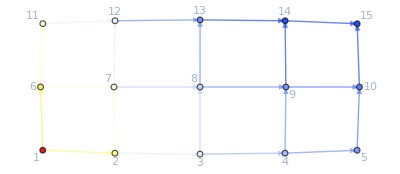

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Reduce[#,Reals]&
```

0≤jt61≤436000/14101&&jt58==(436000-14101 jt61)/14101&&451200/14101≤jt49≤1185600/14101&&jt46==(1185600-14101 jt49)/14101&&606200/14101≤jt37≤1459500/14101&&jt34==(1657100-14101 jt37)/14101&&0≤jt84≤1205900/14101

The error (1-Norm of LHS-RHS) is 9.9476×10^-13

The error is 9.9476×10^-13 which is less than 1.×10^-10

It took 3.79549 seconds to solve!
	The system is 200/7≤jt16≤100

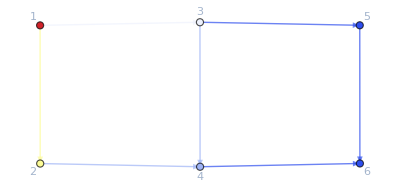

```mathematica
rulesgridsolver = Solver[d2egrid][alpha=1];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgridsolver]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data]
```

```mathematica
d2egrid["EqAllAll"]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

# TestZone

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
```

```mathematica
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
```

```mathematica
Keys[d2egrid]
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,FG,jvars,jtvars,uvars,OutRules,InRules,jays,ExitCosts,AllOr,AllEq,AllIneq,EqAllAll,BoundaryRules,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs}

```mathematica
Length[d2egrid["AllEq"]]
Length[d2egrid["AllEq"]/.rules]
Length[d2egrid["AllOr"]]
Length[d2egrid["AllOr"]/.rules]
Length[d2egrid["AllIneq"]]
Length[d2egrid["AllIneq"]/.rules]
Length[d2egrid["EqCriticalCase"]]
Length[d2egrid["EqCriticalCase"]/.rules]
```

#### This is the winning code!

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

{j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),<|j22→1805500/14101,j24→2840500/14101,u1→141500/239,u26→141500/239|>}

```mathematica
Head/@system
```

GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or

```mathematica
Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jvars"]]
```

{j1≥0&&-3024500/14101+j1≥0&&-3024500/14101+j1≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&(-3024500/14101+j1==0||j1==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),j2≥0&&-2615900/14101+j2≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&(-2615900/14101+j2==0||j2==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0),True,True,True,True,True,True,True,j10≥0&&-1459500/14101+j10≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&j10-jt36-jt37≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&(-1459500/14101+j10==0||j10==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0),j11≥0&&j11≥0&&-19600/239+j11≥0&&-19600/239+j11≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j11≥0&&-19600/239+j11≥0&&j11+j13-j20-jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&(-19600/239+j11==0||j11==0)&&(-19600/239+j11==0||j11==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j12≥0&&-1657100/14101+j12≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&j12-jt48-jt49≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&(-1657100/14101+j12==0||j12==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),j13≥0&&-853300/14101+j13≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&(-853300/14101+j13==0||j13==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j14≥0&&-1185600/14101+j14≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&j14-jt60-jt61≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&(-1185600/14101+j14==0||j14==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),j15≥0&&-1205900/14101+j15≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j15-jt83-jt84≥0&&-1205900/14101+j15-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-1205900/14101+j15==0||j15==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt84==0||-1205900/14101+j15-jt86==0),j16≥0&&-436000/14101+j16≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&(-436000/14101+j16==0||j16==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),j17≥0&&-1430400/14101+j17≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-1430400/14101+j17==0||j17==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),j18≥0&&-994400/14101+j18≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-994400/14101+j18==0||j18==0)&&(j23==0||-994400/14101+j18==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),True,j20≥0&&-2009700/14101+j20≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&j20-j21+jt84-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-2009700/14101+j20==0||j20==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0),j21≥0&&-100+j21≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-100+j21==0||j21==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),True,j23≥0&&j23≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&994400/14101-j18+j23≥0&&(j23==0||j23==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(j23==0||-994400/14101+j18==0),True,True,True,True,True,1973600/14101+j29≥0&&j29≥0&&j29-jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&(j29==0||1973600/14101+j29==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1050900/14101+j30≥0&&j30≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1050900/14101+j30-jt33-jt34≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&(j30==0||1050900/14101+j30==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1239200/14101+j31≥0&&j31≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&(j31==0||1239200/14101+j31==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0),734400/14101+j32≥0&&j32≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&734400/14101+j32-jt45-jt46≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&(j32==0||734400/14101+j32==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),558400/14101+j33≥0&&558400/14101+j33≥0&&j33≥0&&j33≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&(j33==0||558400/14101+j33==0)&&(j33==0||558400/14101+j33==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),680800/14101+j34≥0&&j34≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&680800/14101+j34-jt57-jt58≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&(j34==0||680800/14101+j34==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
NewReduce[And @@ (Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

$Aborted

```mathematica
NewReduce[And@@(Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

```mathematica
FixedPoint
```

```mathematica
system
```

j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&u1≥u26&&0≥-52/7+u1&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)&&(2+j1-j2==0||u1-u26==0)&&(2-j1+j2==0||u1-u26==0)&&(2+j21-j24==0||52/7-u1==0)&&(2-j21+j24==0||52/7-u1==0)

```mathematica
systemgrid
```

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

```mathematica
FreeQ[u1][system]
And@@(FreeQ[#][system]&/@{u1,u2,u3,u4,u5})
```

False

False

```mathematica
FreeQ[#][systemgrid]&/@{u1,u2,u3,u4,u5}
```

{True,True,True,True,True}